# Tentative Fracture/Yield Curves vs. Current Elliptic Ones

Overlays the current elliptic fracture envelope (intact) and yield surface (fractured), from PlasticProjection in simulation/kernels.cu, with tentative piecewise-linear replacements: a Mohr-Coulomb envelope with a tension cutoff (intact), and a cohesionless kinked yield surface (fractured). Edit the constants below and re-evaluate the whole notebook (Evaluate Notebook, in the Evaluation menu).

## Current model constants (edit these)

```mathematica
IceShearStrength = 3.2*10^5;
IceShearStrengthFractured = 1.2*10^5;
IceCompressiveThreshold = 4*10^5;   (* current model's extra crush cutoff -- shown as a reference line only *)
IceTensileStrength = 3.0*10^5;
IceCompressiveStrength = 30*10^6;
DPphi = 55;                         (* degrees *)
DPthresholdP = -300;
```

## Current (elliptic) envelope and yield surface

```mathematica
pminC = -IceTensileStrength;
pmaxC = IceCompressiveStrength;

qEllipse[p_, qmax_] := 2 Sqrt[Max[(pmaxC - p) (p - pminC), 0]] qmax/(pmaxC - pminC);
qIntactCurrent[p_] := If[pminC <= p <= pmaxC, qEllipse[p, IceShearStrength], 0];
qFracCurrent[p_] := If[DPthresholdP <= p <= pmaxC,
   Min[qEllipse[p, IceShearStrengthFractured], Max[0, (p - DPthresholdP) Tan[DPphi Degree]]], 0];
```

## Tentative fracture envelope (Mohr-Coulomb + tension cutoff)

Fits (q0, m) to the current ellipse over an operating window pFitWindow, so the tentative line starts from the existing calibration.

```mathematica
tensileT = IceTensileStrength;         (* T: tensile leg reaches q = 0 at p = -T *)
q0 = qIntactCurrent[0];                (* cohesion intercept, taken from current ellipse at p = 0 *)
pFitWindow = 3*10^5;                   (* fit window for the compression-shear slope *)
mSlope = (qIntactCurrent[pFitWindow] - q0)/pFitWindow;

qFracTentative[p_] := Which[
   p < -tensileT, 0,
   p <= 0, (q0/tensileT) (p + tensileT),
   p <= pmaxC, q0 + mSlope p,
   True, 0];
```

## Tentative yield surface (cohesionless, kinked)

Still q(0) = 0 (cohesionless at zero confinement) -- but the shallow leg needs its own positive intercept qResidual, or Min[] would pick it over the steep leg everywhere (both lines through the origin, shallower always wins). qResidual/mFriction are fit from two points safely past the current model's own DP/ellipse crossover (~p=17000), not from p=0.

```mathematica
mSteep = Tan[DPphi Degree];            (* steep leg through the origin, matches current DP slope *)
pFit1 = 5*10^4;
pFit2 = pFitWindow;
mFriction = (qFracCurrent[pFit2] - qFracCurrent[pFit1])/(pFit2 - pFit1);
qResidual = qFracCurrent[pFit1] - mFriction pFit1;

qYieldTentative[p_] := If[p <= 0, 0, Min[mSteep p, qResidual + mFriction p]];
```

## Cap line (fractured stress never exceeds beta x local intact strength)

```mathematica
betaCap = 0.75;
qCap[p_] := betaCap qFracTentative[p];
```

## Plot

Gray dashed vertical line marks IceCompressiveThreshold (the current model's separate crush cutoff, not part of any curve's shape).

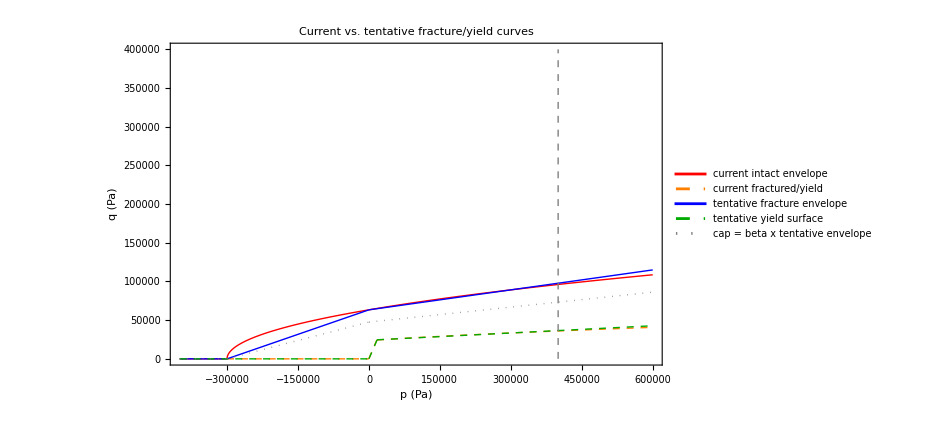

```mathematica
Plot[{qIntactCurrent[p], qFracCurrent[p], qFracTentative[p], qYieldTentative[p], qCap[p]},
  {p, -4*10^5, 6*10^5},
  PlotRange -> {{-4*10^5, 6*10^5}, {0, 4*10^5}},
  PlotStyle -> {Directive[Red, Thick], Directive[Orange, Thick, Dashed],
    Directive[Blue, Thick], Directive[Darker[Green], Thick, Dashed],
    Directive[Gray, Thin, Dotted]},
  PlotLegends -> {"current intact envelope", "current fractured/yield",
    "tentative fracture envelope", "tentative yield surface",
    "cap = beta x tentative envelope"},
  Frame -> True, FrameLabel -> {"p  (Pa)", "q  (Pa)"},
  PlotLabel -> "Current vs. tentative fracture/yield curves",
  Epilog -> {Gray, Dashed, Line[{{IceCompressiveThreshold, 0}, {IceCompressiveThreshold, 4*10^5}}]},
  ImageSize -> 700, PlotPoints -> 300]
```